```mathematica
ClearAll["Global`*"];
```

```mathematica
a=1;
f = s^(a-1)Exp[-x s^a];
InverseLaplaceTransform[f,s,t]
```

1

DiracDelta[t-x]

### Parameters

## Calculate Inverse Laplace with GWR

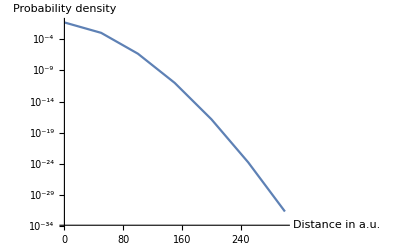

```mathematica
<<NumericalLaplaceInversion.m
<<FixedTalbotNumericalLaplaceInversion.m
a = 4/10;
xMin = 0; xMax =20000; xSteps = 400; t0 =500;
xValues = Subdivide[xMin,xMax,xSteps];
yValues = Table[
F[s_] = s^(a-1)Exp[-x s^a];(*s^-a*)
GWR[F,t0],
{x,xValues}];
data = Transpose[{xValues,yValues}];
boundary = {{t0^a,Abs[Min[yValues]]},{t0^a,Max[yValues]}};
ListLogPlot[{data},Joined->True,AxesLabel->{"Distance in a.u.","Probability density"}](*Export["MA/CUDA_Simulation_RW/Results/InverseLaplace/InverseLaplace_a_"<> ToString[ N[a]]<> "_t_" <>ToString[t0]<>".txt",{N[xValues],N[yValues]},"Table","FieldSeparators"->" "]*)
```

```mathematica
N[1/2]
```

MA/CUDA_Simulation_RW/Results/InverseLaplace/InverseLaplace_a_1.2_t_1000.txt

0.5

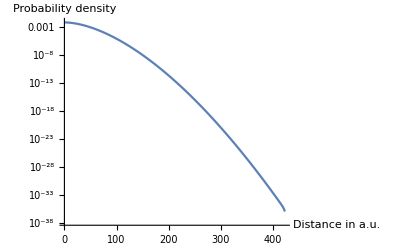

```mathematica
ListLogPlot[{data},Joined->True,AxesLabel->{"Distance in a.u.","Probability density"}]
```

-1.19673244623050682108183975009000613×10^-35

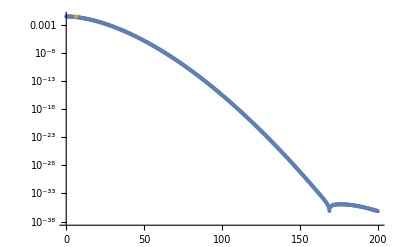

```mathematica
Min[yValues]
ListLogPlot[{Abs[data],boundary}]
```

## Calculate Inverse Laplace with Talbot

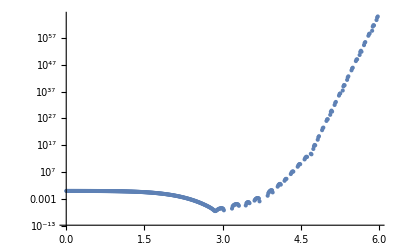

```mathematica
<<FixedTalbotNumericalLaplaceInversion.m
yValues = Table[
F[s_] = s^-a Exp[-x s^a];
FT[F,t0],
{x,xValues}];
data = Transpose[{xValues,yValues}];
ListLogPlot[data]
```

## Test if a = 1/2 gives Gaus distribution

```mathematica
yLogValues  = Log[yValues];
logData = Transpose[{xValues,yLogValues}];
dataPlot=ListPlot[logData];
fit = Fit[yLogValues,{t^2,1},t]; 
fn[x_] = -1/2-4.1/16 t^2;
fitPlot = Plot[fn[t],{t,xMin,xMax}];
Show[dataPlot,fitPlot]
```